## Euler-Poisson

## Numeric Intro (Dzhanibekov)

```mathematica
EP1=With[{I1=13/3 48,I2=10/3 48,I3=5/3 48},{ω1'[t]+(I3-I2)/I1 ω2[t]ω3[t]==0,ω2'[t]+(I1-I3)/I2 ω3[t]ω1[t]==0,ω3'[t]+(I2-I1)/I3 ω1[t]ω2[t]==0}]
```

{-5/13 ω2[t] ω3[t]+ω1'[t]==0,4/5 ω1[t] ω3[t]+ω2'[t]==0,-3/5 ω1[t] ω2[t]+ω3'[t]==0}

```mathematica
IC1={ω1[0]==1/100,ω2[0]==1,ω3[0]==1/100};
```

```mathematica
ble[t_]={ω1[t],ω2[t],ω3[t]}/.NDSolve[Join[EP1,IC1],{ω1[t],ω2[t],ω3[t]},{t,0,100}][[1]];
```

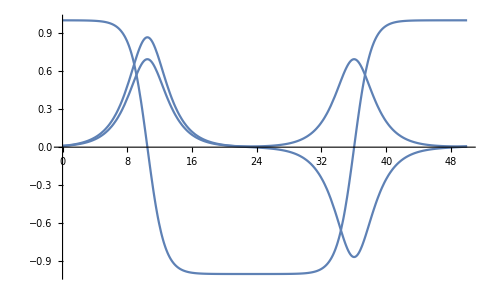

```mathematica
Plot[ble[t],{t,0,50}]
```

```mathematica
EP2=Thread[Flatten[Q'[t]-Q[t].Ω[t]]==0];
IC2=Thread[Flatten[Q[0]-IdentityMatrix[3]]==0];
```

```mathematica
{qble2[t_],oble2[t_]}={Q[t],ω[t]}/.NDSolve[Join[EP1,IC1,EP2,IC2],Join[ω[t],Flatten[Q[t]]],{t,0,100}][[1]];
```

```mathematica
grp=ParametricPlot3D[qble2[t][[;;,2]],{t,0,100},PlotStyle->{Thin,ColorData[97][2]},PlotRange->All];
```

```mathematica
Animate[Graphics3D[{First[grp],MapIndexed[{v,i}↦{Thick,ColorData[97][i[[1]]],Arrow[{{0,0,0},v}]},qble2[t]ᵀ]},PlotRange->{{-1,1},{-1,1},{-1,1}}],{t,0,50,.1},DisplayAllSteps->True,AnimationRate->10,AnimationRunning->False]
```

## Derivation

```mathematica
𝟙=IdentityMatrix[3];
Q[t_]=({{q11[t], q12[t], q13[t]}, {q21[t], q22[t], q23[t]}, {q31[t], q32[t], q33[t]}});
Ω[t_]=({{0, -ω3[t], +ω2[t]}, {+ω3[t], 0, -ω1[t]}, {-ω2[t], +ω1[t], 0}});
ω[t_]={ω1[t],ω2[t],ω3[t]};
Ω[t]==-Normal@HodgeDual[ω[t]]
Ω[t].{x,y,z}-ω[t]×{x,y,z}
```

True

{0,0,0}

```mathematica
J0=m {x,y,z}⊗{x,y,z};
𝒯0=m{x,y,z}.Ω[t]ᵀ.Ω[t].{x,y,z}//Simplify
(J1=1/2 D[𝒯0,{ω[t]},{ω[t]}]//Simplify)//MatrixForm
ω[t].J1.ω[t]==m{x,y,z}.Ω[t]ᵀ.Ω[t].{x,y,z}//Simplify
J1==m{x,y,z}.{x,y,z}𝟙-J0//Simplify
```

m ((y^2+z^2) ω1[t]^2+(x^2+z^2) ω2[t]^2-2 y z ω2[t] ω3[t]+(x^2+y^2) ω3[t]^2-2 x ω1[t] (y ω2[t]+z ω3[t]))

(m (y^2+z^2) | -m x y | -m x z
-m x y | m (x^2+z^2) | -m y z
-m x z | -m y z | m (x^2+y^2))

True

True

```mathematica
Λ=({{λ11, λ12, λ13}, {λ12, λ22, λ23}, {λ13, λ23, λ33}})(*1/2(({{λ11, λ12, λ13}, {λ21, λ22, λ23}, {λ31, λ32, λ33}})+({{λ11, λ12, λ13}, {λ21, λ22, λ23}, {λ31, λ32, λ33}})ᵀ)*);
```

```mathematica
𝒯=1/2 m{x,y,z}.Q'[t]ᵀ.Q'[t].{x,y,z}//Simplify
ℒ=𝒯-Tr[Λᵀ.(Q[t]ᵀ.Q[t]-𝟙)]
```

1/2 m (x^2 q11'[t]^2+y^2 q12'[t]^2+2 y z q12'[t] q13'[t]+z^2 q13'[t]^2+2 x q11'[t] (y q12'[t]+z q13'[t])+x^2 q21'[t]^2+2 x y q21'[t] q22'[t]+y^2 q22'[t]^2+2 x z q21'[t] q23'[t]+2 y z q22'[t] q23'[t]+z^2 q23'[t]^2+x^2 q31'[t]^2+2 x y q31'[t] q32'[t]+y^2 q32'[t]^2+2 x z q31'[t] q33'[t]+2 y z q32'[t] q33'[t]+z^2 q33'[t]^2)

-λ11 (-1+q11[t]^2+q21[t]^2+q31[t]^2)-2 λ12 (q11[t] q12[t]+q21[t] q22[t]+q31[t] q32[t])-λ22 (-1+q12[t]^2+q22[t]^2+q32[t]^2)-2 λ13 (q11[t] q13[t]+q21[t] q23[t]+q31[t] q33[t])-2 λ23 (q12[t] q13[t]+q22[t] q23[t]+q32[t] q33[t])-λ33 (-1+q13[t]^2+q23[t]^2+q33[t]^2)+1/2 m (x^2 q11'[t]^2+y^2 q12'[t]^2+2 y z q12'[t] q13'[t]+z^2 q13'[t]^2+2 x q11'[t] (y q12'[t]+z q13'[t])+x^2 q21'[t]^2+2 x y q21'[t] q22'[t]+y^2 q22'[t]^2+2 x z q21'[t] q23'[t]+2 y z q22'[t] q23'[t]+z^2 q23'[t]^2+x^2 q31'[t]^2+2 x y q31'[t] q32'[t]+y^2 q32'[t]^2+2 x z q31'[t] q33'[t]+2 y z q32'[t] q33'[t]+z^2 q33'[t]^2)

```mathematica
qosol1=Flatten@MapThread[Rule,{Q'[t],Q[t].Ω[t]},2]
```

{q11'[t]→-q13[t] ω2[t]+q12[t] ω3[t],q12'[t]→q13[t] ω1[t]-q11[t] ω3[t],q13'[t]→-q12[t] ω1[t]+q11[t] ω2[t],q21'[t]→-q23[t] ω2[t]+q22[t] ω3[t],q22'[t]→q23[t] ω1[t]-q21[t] ω3[t],q23'[t]→-q22[t] ω1[t]+q21[t] ω2[t],q31'[t]→-q33[t] ω2[t]+q32[t] ω3[t],q32'[t]→q33[t] ω1[t]-q31[t] ω3[t],q33'[t]→-q32[t] ω1[t]+q31[t] ω2[t]}

```mathematica
Q''[t]-D[Q[t].Ω[t],t]/.qosol1//Simplify;
qosol2=Solve[%==0,Flatten[Q''[t]]][[1]]//Simplify;
Q''[t]==Q[t].(Ω[t].Ω[t]+Ω'[t])/.qosol2//Simplify
```

True

```mathematica
D[D[ℒ,{Flatten[Q'[t]]}],t]//Simplify;
EL1=Partition[%,3];
EL1==Q''[t].J0//Simplify
```

True

```mathematica
D[ℒ,{Flatten[Q[t]]}]//Simplify;
EL2=Partition[%,3];
EL2==-2Q[t].Λ//FullSimplify
```

True

```mathematica
(Q''[t].J0+2Q[t].Λ)
%==(EL1-EL2)//Simplify
```

{{2 (λ11 q11[t]+λ12 q12[t]+λ13 q13[t])+m x^2 q11''[t]+m x y q12''[t]+m x z q13''[t],2 (λ12 q11[t]+λ22 q12[t]+λ23 q13[t])+m x y q11''[t]+m y^2 q12''[t]+m y z q13''[t],2 (λ13 q11[t]+λ23 q12[t]+λ33 q13[t])+m x z q11''[t]+m y z q12''[t]+m z^2 q13''[t]},{2 (λ11 q21[t]+λ12 q22[t]+λ13 q23[t])+m x^2 q21''[t]+m x y q22''[t]+m x z q23''[t],2 (λ12 q21[t]+λ22 q22[t]+λ23 q23[t])+m x y q21''[t]+m y^2 q22''[t]+m y z q23''[t],2 (λ13 q21[t]+λ23 q22[t]+λ33 q23[t])+m x z q21''[t]+m y z q22''[t]+m z^2 q23''[t]},{2 (λ11 q31[t]+λ12 q32[t]+λ13 q33[t])+m x^2 q31''[t]+m x y q32''[t]+m x z q33''[t],2 (λ12 q31[t]+λ22 q32[t]+λ23 q33[t])+m x y q31''[t]+m y^2 q32''[t]+m y z q33''[t],2 (λ13 q31[t]+λ23 q32[t]+λ33 q33[t])+m x z q31''[t]+m y z q32''[t]+m z^2 q33''[t]}}

True

```mathematica
With[{J0=DiagonalMatrix[{jx,jy,jz}]},J0.Ω[t]ᵀ.Ω[t].J0-(J0.Λ+Λ.J0)//Simplify]
jsol=Solve[%==0,Flatten[Λ]][[1]]//Simplify
```

{{jx (-2 λ11+jx ω2[t]^2+jx ω3[t]^2),-((jx+jy) λ12)-jx jy ω1[t] ω2[t],-((jx+jz) λ13)-jx jz ω1[t] ω3[t]},{-((jx+jy) λ12)-jx jy ω1[t] ω2[t],jy (-2 λ22+jy ω1[t]^2+jy ω3[t]^2),-((jy+jz) λ23)-jy jz ω2[t] ω3[t]},{-((jx+jz) λ13)-jx jz ω1[t] ω3[t],-((jy+jz) λ23)-jy jz ω2[t] ω3[t],jz (-2 λ33+jz ω1[t]^2+jz ω2[t]^2)}}

{λ11→1/2 jx (ω2[t]^2+ω3[t]^2),λ12→-(jx jy ω1[t] ω2[t])/(jx+jy),λ13→-(jx jz ω1[t] ω3[t])/(jx+jz),λ22→1/2 jy (ω1[t]^2+ω3[t]^2),λ23→-(jy jz ω2[t] ω3[t])/(jy+jz),λ33→1/2 jz (ω1[t]^2+ω2[t]^2)}

```mathematica
With[{J0=DiagonalMatrix[{jx,jy,jz}]},(Ω[t].Ω[t]+Ω'[t]).J0+2Λ/.jsol]//FullSimplify
Solve[%==0,ω'[t]]⟦1⟧//Simplify
%/.{jx->(Subscript[ℐ, y]+Subscript[ℐ, z]-Subscript[ℐ, x])/2,jy->(-Subscript[ℐ, y]+Subscript[ℐ, z]+Subscript[ℐ, x])/2,jz->(Subscript[ℐ, y]-Subscript[ℐ, z]+Subscript[ℐ, x])/2}//Simplify
```

{{0,(jy (-jx+jy) ω1[t] ω2[t])/(jx+jy)-jy ω3'[t],jz (((-jx+jz) ω1[t] ω3[t])/(jx+jz)+ω2'[t])},{jx (((jx-jy) ω1[t] ω2[t])/(jx+jy)+ω3'[t]),0,(jz (-jy+jz) ω2[t] ω3[t])/(jy+jz)-jz ω1'[t]},{(jx (jx-jz) ω1[t] ω3[t])/(jx+jz)-jx ω2'[t],jy (((jy-jz) ω2[t] ω3[t])/(jy+jz)+ω1'[t]),0}}

{ω1'[t]→((-jy+jz) ω2[t] ω3[t])/(jy+jz),ω2'[t]→((jx-jz) ω1[t] ω3[t])/(jx+jz),ω3'[t]→((-jx+jy) ω1[t] ω2[t])/(jx+jy)}

{ω1'[t]→((ℐ_y-ℐ_z) ω2[t] ω3[t])/ℐ_x,ω2'[t]→-((ℐ_x-ℐ_z) ω1[t] ω3[t])/ℐ_y,ω3'[t]→((ℐ_x-ℐ_y) ω1[t] ω2[t])/ℐ_z}

### +Gravity

```mathematica
GR={γx,γy,γz}⊗{cx,cy,cz};
```

```mathematica
With[{J0=DiagonalMatrix[{jx,jy,jz}]},J0.Ω[t]ᵀ.Ω[t].J0-1/2(J0.GR+GRᵀ.J0)-(J0.Λ+Λ.J0)//Simplify]
Solve[%==0,Flatten[Λ]][[1]]//FullSimplify
With[{J0=DiagonalMatrix[{jx,jy,jz}]},Ω'[t].J0+(GR+2Λ)+Ω[t].Ω[t].J0]/.%/.{jx->(Subscript[ℐ, y]+Subscript[ℐ, z]-Subscript[ℐ, x])/2,jy->(-Subscript[ℐ, y]+Subscript[ℐ, z]+Subscript[ℐ, x])/2,jz->(Subscript[ℐ, y]-Subscript[ℐ, z]+Subscript[ℐ, x])/2}//FullSimplify//MatrixForm
Column@Collect[Normal@HodgeDual[2%],ω'[t],FullSimplify]
```

{{jx (-cx γx-2 λ11+jx ω2[t]^2+jx ω3[t]^2),1/2 (-cy jx γx-cx jy γy-2 jx λ12-2 jy λ12-2 jx jy ω1[t] ω2[t]),1/2 (-cz jx γx-cx jz γz-2 jx λ13-2 jz λ13-2 jx jz ω1[t] ω3[t])},{1/2 (-cy jx γx-cx jy γy-2 jx λ12-2 jy λ12-2 jx jy ω1[t] ω2[t]),jy (-cy γy-2 λ22+jy ω1[t]^2+jy ω3[t]^2),1/2 (-cz jy γy-cy jz γz-2 jy λ23-2 jz λ23-2 jy jz ω2[t] ω3[t])},{1/2 (-cz jx γx-cx jz γz-2 jx λ13-2 jz λ13-2 jx jz ω1[t] ω3[t]),1/2 (-cz jy γy-cy jz γz-2 jy λ23-2 jz λ23-2 jy jz ω2[t] ω3[t]),jz (-cz γz-2 λ33+jz ω1[t]^2+jz ω2[t]^2)}}

{λ11→1/2 (-cx γx+jx (ω2[t]^2+ω3[t]^2)),λ12→-(cy jx γx+cx jy γy+2 jx jy ω1[t] ω2[t])/(2 (jx+jy)),λ13→-(cz jx γx+cx jz γz+2 jx jz ω1[t] ω3[t])/(2 (jx+jz)),λ22→1/2 (-cy γy+jy (ω1[t]^2+ω3[t]^2)),λ23→-(cz jy γy+cy jz γz+2 jy jz ω2[t] ω3[t])/(2 (jy+jz)),λ33→1/2 (-cz γz+jz (ω1[t]^2+ω2[t]^2))}

(0 | ((ℐ_x-ℐ_y+ℐ_z) (cy γx-cx γy+(ℐ_x-ℐ_y) ω1[t] ω2[t]-ℐ_z ω3'[t]))/(2 ℐ_z) | ((ℐ_x+ℐ_y-ℐ_z) (cz γx-cx γz+(ℐ_x-ℐ_z) ω1[t] ω3[t]+ℐ_y ω2'[t]))/(2 ℐ_y)
((ℐ_x-ℐ_y-ℐ_z) (cy γx-cx γy+(ℐ_x-ℐ_y) ω1[t] ω2[t]-ℐ_z ω3'[t]))/(2 ℐ_z) | 0 | -((ℐ_x+ℐ_y-ℐ_z) (-cz γy+cy γz+(-ℐ_y+ℐ_z) ω2[t] ω3[t]+ℐ_x ω1'[t]))/(2 ℐ_x)
-((-ℐ_x+ℐ_y+ℐ_z) (cz γx-cx γz+(ℐ_x-ℐ_z) ω1[t] ω3[t]+ℐ_y ω2'[t]))/(2 ℐ_y) | ((ℐ_x-ℐ_y+ℐ_z) (-cz γy+cy γz+(-ℐ_y+ℐ_z) ω2[t] ω3[t]+ℐ_x ω1'[t]))/(2 ℐ_x) | 0)

cz γy-cy γz+(ℐ_y-ℐ_z) ω2[t] ω3[t]-ℐ_x ω1'[t]
-cz γx+cx γz+(-ℐ_x+ℐ_z) ω1[t] ω3[t]-ℐ_y ω2'[t]
cy γx-cx γy+(ℐ_x-ℐ_y) ω1[t] ω2[t]-ℐ_z ω3'[t]

```mathematica
(GR-GRᵀ)//Simplify//MatrixForm
```

(0 | cy γx-cx γy | cz γx-cx γz
-cy γx+cx γy | 0 | cz γy-cy γz
-cz γx+cx γz | -cz γy+cy γz | 0)

```mathematica
Normal[{γx,γy,γz}\[TensorWedge]{cx,cy,cz}]//MatrixForm
```

(0 | cy γx-cx γy | cz γx-cx γz
-cy γx+cx γy | 0 | cz γy-cy γz
-cz γx+cx γz | -cz γy+cy γz | 0)

```mathematica
{γx,γy,γz}×{cx,cy,cz}
GR-GRᵀ==HodgeDual[%]
```

{cz γy-cy γz,-cz γx+cx γz,cy γx-cx γy}

True

```mathematica
Normal@HodgeDual[ω[t]]
```

{{0,ω3[t],-ω2[t]},{-ω3[t],0,ω1[t]},{ω2[t],-ω1[t],0}}

## Numerical Tetratop

```mathematica
𝒯4=Tetrahedron[{{0,0,0},{1,0,1},{-1/2,(√3)/2,1},{-1/2,(-√3)/2,1}}];
(*𝒯4=Tetrahedron[];*)
CM=1/Volume[𝒯4] Integrate[{x,y,z},{x,y,z}∈Region[𝒯4]]
J1T=Integrate[J1/m,{x,y,z}∈𝒯4]
```

{0,0,3/4}

{{(27 √3)/160,0,0},{0,(27 √3)/160,0},{0,0,(3 √3)/80}}

```mathematica
Map[p↦Norm[p-CM]//N,{{0,0,0},{1,0,1},{-1/2,(√3)/2,1},{-1/2,(-√3)/2,1}}]
```

{0.75,1.03078,1.03078,1.03078}

```mathematica
Graphics3D[{Red,Opacity[.5],𝒯4,Black,PointSize[0.02],Point[{CM}]},PlotRange->{{-1,1},{-1,1},{0,1.1}},Axes->True,BoxRatios->{2,2,1.1}]
```

-Graphics3D-

```mathematica
EP1=With[{I1=J1T[[1,1]],I2=J1T[[2,2]],I3=J1T[[3,3]],γ=Q[t]ᵀ.{0,0,-1},g=10},{I1 ω1'[t]==g(γ×CM)[[1]]+(I2-I3) ω2[t] ω3[t],I2 ω2'[t]==g(γ×CM)[[2]]+(I3-I1)ω3[t]ω1[t],ω3'[t]==g(γ×CM)[[3]]+(I1-I3)ω1[t]ω2[t]}]
```

{27/160 √3 ω1'[t]==-(15 q32[t])/2+21/160 √3 ω2[t] ω3[t],27/160 √3 ω2'[t]==(15 q31[t])/2-21/160 √3 ω1[t] ω3[t],ω3'[t]==21/160 √3 ω1[t] ω2[t]}

```mathematica
IC1={ω1[0]==1/1,ω2[0]==1/1,ω3[0]==100/1};
```

```mathematica
EP2=Thread[Flatten[Q'[t]-Q[t].Ω[t]]==0];
IC2=With[{α=π/5},Thread[Flatten[Q[0]-({{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}})]==0]];
```

```mathematica
{qble2[t_],oble2[t_]}={Q[t],ω[t]}/.NDSolve[Join[EP1,IC1,EP2,IC2],Join[ω[t],Flatten[Q[t]]],{t,0,100}][[1]];
```

```mathematica
grp=ParametricPlot3D[1.5qble2[t][[;;,3]],{t,0,5.73},PlotStyle->{ColorData[97][3]},PlotRange->All]
```

```mathematica
TQ[t_]=Tetrahedron[{{0,0,0},{1,0,1},{-1/2,(√3)/2,1},{-1/2,(-√3)/2,1}}.qble2[t]ᵀ];
```

```mathematica
With[{t=.8},Show[grp,Graphics3D[{{Red,Opacity[.9],TQ[t]},MapIndexed[{v,i}↦{Thick,ColorData[97][i[[1]]],Arrow[{{0,0,0},v}]},1.5qble2[t]ᵀ]}],PlotRange->{1.2{-1,1},1.2{-1,1},{0,1.7}},BoxRatios->Automatic,ImageSize->400]]
```

```mathematica
Dynamic[t//N]
```

```mathematica
Do[Export["/home/tomasz/klatka/tt"<>IntegerString[1000t,10,4]<>".png",Show[grp,Graphics3D[{{Red,Opacity[.9],TQ[t]},{Thick,Arrow[{{0,0,0},1.5qble2[t][[;;,3]]}]}}],PlotRange->{1.2{-1,1},1.2{-1,1},{0,1.7}},ImageSize->600],ImageSize->{600,600}],{t,999/1000,2000/1000,1/1000}]
```

```mathematica
ListAnimate[ttt1,DisplayAllSteps->True,AnimationRunning->False]
```